```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=200;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->20},PlotRange->{0,1.1}]
```

Table::iterb: 反復演算{t,1,bit}は適正な範囲を持ちません．

Table[digital[t],{t,1,bit}]

Plot::plln: {t,0,25 bit}の範囲指定値25 bitは機械サイズの実数ではありません．

Plot[signal[t/10^12],{t,0,bit 25},PlotStyle→{Red,Thick},Frame→True,FrameLabel→{Time[ps],Power},BaseStyle→{Bold,FontSize→20},PlotRange→{0,1.1}]

1/2 (1+Cos[400000000000000 π t])

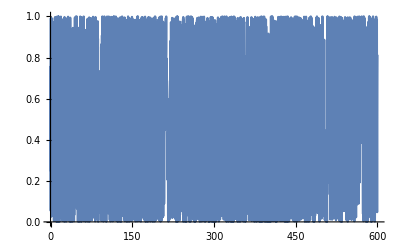

1/2 (1+Cos[400000000000000 π t]) (If[1/40000000000<t<1/20000000000,0,0]+If[1/20000000000<t<3/40000000000,1,0]+If[3/40000000000<t<1/10000000000,0,0]+If[1/10000000000<t<1/8000000000,1,0]+If[1/8000000000<t<3/20000000000,1,0]+If[3/20000000000<t<7/40000000000,0,0]+If[7/40000000000<t<1/5000000000,1,0]+If[1/5000000000<t<9/40000000000,1,0]+If[9/40000000000<t<1/4000000000,1,0]+If[1/4000000000<t<11/40000000000,0,0]+If[11/40000000000<t<3/10000000000,0,0]+If[3/10000000000<t<13/40000000000,0,0]+If[13/40000000000<t<7/20000000000,1,0]+If[7/20000000000<t<3/8000000000,0,0]+If[3/8000000000<t<1/2500000000,0,0]+If[1/2500000000<t<17/40000000000,1,0]+If[17/40000000000<t<9/20000000000,0,0]+If[9/20000000000<t<19/40000000000,0,0]+If[19/40000000000<t<1/2000000000,1,0]+If[1/2000000000<t<21/40000000000,1,0]+If[21/40000000000<t<11/20000000000,0,0]+If[11/20000000000<t<23/40000000000,1,0]+If[23/40000000000<t<3/5000000000,1,0]+If[3/5000000000<t<1/1600000000,1,0]+If[1/1600000000<t<13/20000000000,1,0])

```mathematica
Fc= 200 *10^12;(*搬送波の周波数[THz]*)
carrier[t]= (Cos[2*Pi*Fc*t]+1)/2
Plot[carrier[t], {t,0,600}]
cs[t_]=signal[t]*carrier[t]
```

```mathematica
∫_0^(bit*25*10^-12) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))

```mathematica
fc[f_]:=-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))
```

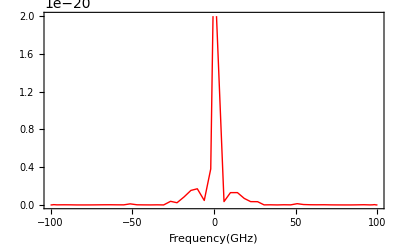

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-1*^2,1*^2},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

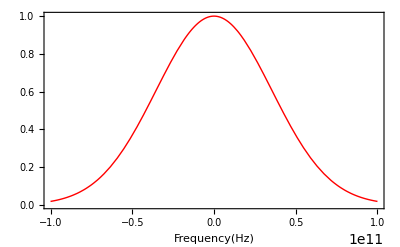

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

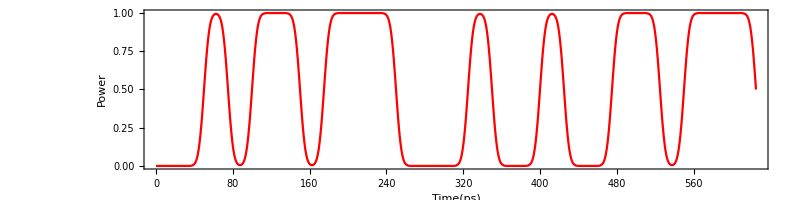

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
(*f[x_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]*)
```

```mathematica
(*max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]*)
```

## Impulse Responce for Fiber Dispersion

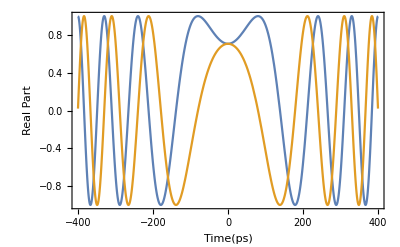

```mathematica
hdis[t_]:=(*1/(√(2*Pi*β2*L))*10^6**)Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-12],Im@hdis[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
(*hcmp[t_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(t^2/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(t^2/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]*)
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
(*For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]*)
```

```mathematica
(*IntegerPart[total*10^12]*)
```

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
(*For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]*)
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

-Graphics-

## Simulation

```mathematica
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*hdis2[a-t],{t,-100,25*bit+100,samp}]
```

```mathematica
simu1[-100.]
```

-1.29213+49.9432 ⅈ

```mathematica
For[i=-100.,i≤25*bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

150.

200.

250.

300.

350.

400.

450.

500.

550.

600.

650.

700.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,25*bit+100,samp}]
```

{{-100.,49.9599},{-99.5,50.4628},{-99.,50.9715},{-98.5,51.4855},{-98.,52.0044},{-97.5,52.5278},{-97.,53.0551},{-96.5,53.5859},{-96.,54.1198},{-95.5,54.6563},{-95.,55.195},{-94.5,55.7354},{-94.,56.2772},{-93.5,56.8198},{-93.,57.3628},{-92.5,57.9059},{-92.,58.4487},{-91.5,58.9908},{-91.,59.5317},{-90.5,60.0712},{-90.,60.6088},{-89.5,61.1443},{-89.,61.6773},{-88.5,62.2075},{-88.,62.7346},{-87.5,63.2583},{-87.,63.7783},{-86.5,64.2943},{-86.,64.8061},{-85.5,65.3134},{-85.,65.816},{-84.5,66.3138},{-84.,66.8063},{-83.5,67.2935},{-83.,67.7752},{-82.5,68.2511},{-82.,68.7211},{-81.5,69.185},{-81.,69.6426},{-80.5,70.0938},{-80.,70.5384},{-79.5,70.9761},{-79.,71.4069},{-78.5,71.8306},{-78.,72.247},{-77.5,72.656},{-77.,73.0573},{-76.5,73.4508},{-76.,73.8363},{-75.5,74.2136},{-75.,74.5825},{-74.5,74.9429},{-74.,75.2943},{-73.5,75.6367},{-73.,75.9698},{-72.5,76.2933},{-72.,76.607},{-71.5,76.9105},{-71.,77.2035},{-70.5,77.4857},{-70.,77.7569},{-69.5,78.0165},{-69.,78.2642},{-68.5,78.4997},{-68.,78.7224},{-67.5,78.9321},{-67.,79.1282},{-66.5,79.3102},{-66.,79.4776},{-65.5,79.6301},{-65.,79.7669},{-64.5,79.8877},{-64.,79.9917},{-63.5,80.0785},{-63.,80.1476},{-62.5,80.1982},{-62.,80.2297},{-61.5,80.2417},{-61.,80.2334},{-60.5,80.2042},{-60.,80.1536},{-59.5,80.0807},{-59.,79.9852},{-58.5,79.8662},{-58.,79.7233},{-57.5,79.5557},{-57.,79.3629},{-56.5,79.1443},{-56.,78.8993},{-55.5,78.6274},{-55.,78.328},{-54.5,78.0006},{-54.,77.6449},{-53.5,77.2602},{-53.,76.8463},{-52.5,76.4027},{-52.,75.9292},{-51.5,75.4255},{-51.,74.8914},{-50.5,74.3268},{-50.,73.7316},{-49.5,73.1057},{-49.,72.4494},{-48.5,71.7627},{-48.,71.0459},{-47.5,70.2994},{-47.,69.5237},{-46.5,68.7195},{-46.,67.8873},{-45.5,67.0283},{-45.,66.1433},{-44.5,65.2337},{-44.,64.3009},{-43.5,63.3465},{-43.,62.3724},{-42.5,61.3808},{-42.,60.3739},{-41.5,59.3545},{-41.,58.3256},{-40.5,57.2906},{-40.,56.2533},{-39.5,55.2177},{-39.,54.1886},{-38.5,53.1709},{-38.,52.1702},{-37.5,51.1928},{-37.,50.2451},{-36.5,49.3344},{-36.,48.4683},{-35.5,47.655},{-35.,46.9032},{-34.5,46.2218},{-34.,45.62},{-33.5,45.1071},{-33.,44.6921},{-32.5,44.3838},{-32.,44.1905},{-31.5,44.1195},{-31.,44.1771},{-30.5,44.3684},{-30.,44.6968},{-29.5,45.1644},{-29.,45.7717},{-28.5,46.5175},{-28.,47.3995},{-27.5,48.4139},{-27.,49.5558},{-26.5,50.8196},{-26.,52.199},{-25.5,53.6872},{-25.,55.2772},{-24.5,56.9619},{-24.,58.7341},{-23.5,60.5868},{-23.,62.513},{-22.5,64.5063},{-22.,66.5601},{-21.5,68.6683},{-21.,70.8251},{-20.5,73.0248},{-20.,75.2621},{-19.5,77.5319},{-19.,79.8293},{-18.5,82.1498},{-18.,84.4889},{-17.5,86.8423},{-17.,89.2059},{-16.5,91.5759},{-16.,93.9485},{-15.5,96.3201},{-15.,98.6871},{-14.5,101.046},{-14.,103.394},{-13.5,105.728},{-13.,108.044},{-12.5,110.339},{-12.,112.611},{-11.5,114.857},{-11.,117.074},{-10.5,119.26},{-10.,121.411},{-9.5,123.525},{-9.,125.6},{-8.5,127.633},{-8.,129.622},{-7.5,131.565},{-7.,133.459},{-6.5,135.302},{-6.,137.093},{-5.5,138.828},{-5.,140.507},{-4.5,142.127},{-4.,143.686},{-3.5,145.182},{-3.,146.615},{-2.5,147.982},{-2.,149.281},{-1.5,150.512},{-1.,151.672},{-0.5,152.76},{0.,153.776},{0.5,154.717},{1.,155.583},{1.5,156.372},{2.,157.084},{2.5,157.717},{3.,158.272},{3.5,158.746},{4.,159.139},{4.5,159.451},{5.,159.681},{5.5,159.829},{6.,159.893},{6.5,159.875},{7.,159.774},{7.5,159.589},{8.,159.321},{8.5,158.969},{9.,158.534},{9.5,158.016},{10.,157.415},{10.5,156.732},{11.,155.966},{11.5,155.119},{12.,154.192},{12.5,153.183},{13.,152.096},{13.5,150.93},{14.,149.686},{14.5,148.366},{15.,146.97},{15.5,145.499},{16.,143.955},{16.5,142.34},{17.,140.653},{17.5,138.898},{18.,137.075},{18.5,135.186},{19.,133.233},{19.5,131.217},{20.,129.14},{20.5,127.004},{21.,124.811},{21.5,122.562},{22.,120.26},{22.5,117.907},{23.,115.505},{23.5,113.056},{24.,110.562},{24.5,108.025},{25.,105.448},{25.5,102.833},{26.,100.183},{26.5,97.4985},{27.,94.7834},{27.5,92.0396},{28.,89.2697},{28.5,86.476},{29.,83.661},{29.5,80.8272},{30.,77.977},{30.5,75.1131},{31.,72.2377},{31.5,69.3536},{32.,66.4631},{32.5,63.5689},{33.,60.6734},{33.5,57.7792},{34.,54.8889},{34.5,52.0051},{35.,49.1305},{35.5,46.2678},{36.,43.4199},{36.5,40.5897},{37.,37.7805},{37.5,34.9959},{38.,32.2398},{38.5,29.5171},{39.,26.8336},{39.5,24.1968},{40.,21.6167},{40.5,19.1076},{41.,16.6908},{41.5,14.3993},{42.,12.287},{42.5,10.4429},{43.,9.00857},{43.5,8.17492},{44.,8.1013},{44.5,8.78127},{45.,10.041},{45.5,11.6758},{46.,13.5348},{46.5,15.5243},{47.,17.5889},{47.5,19.6955},{48.,21.8239},{48.5,23.9617},{49.,26.1009},{49.5,28.2369},{50.,30.3666},{50.5,32.4888},{51.,34.6028},{51.5,36.709},{52.,38.8081},{52.5,40.9014},{53.,42.9905},{53.5,45.0772},{54.,47.1637},{54.5,49.2522},{55.,51.3453},{55.5,53.4456},{56.,55.5557},{56.5,57.6783},{57.,59.8163},{57.5,61.9726},{58.,64.1498},{58.5,66.351},{59.,68.5787},{59.5,70.8357},{60.,73.1247},{60.5,75.4481},{61.,77.8083},{61.5,80.2076},{62.,82.6481},{62.5,85.1318},{63.,87.6604},{63.5,90.2355},{64.,92.8585},{64.5,95.5307},{65.,98.253},{65.5,101.026},{66.,103.851},{66.5,106.727},{67.,109.656},{67.5,112.636},{68.,115.669},{68.5,118.752},{69.,121.886},{69.5,125.069},{70.,128.301},{70.5,131.581},{71.,134.906},{71.5,138.276},{72.,141.688},{72.5,145.14},{73.,148.632},{73.5,152.159},{74.,155.721},{74.5,159.314},{75.,162.935},{75.5,166.583},{76.,170.255},{76.5,173.947},{77.,177.656},{77.5,181.379},{78.,185.114},{78.5,188.856},{79.,192.604},{79.5,196.352},{80.,200.098},{80.5,203.839},{81.,207.57},{81.5,211.289},{82.,214.992},{82.5,218.675},{83.,222.334},{83.5,225.967},{84.,229.569},{84.5,233.136},{85.,236.666},{85.5,240.155},{86.,243.598},{86.5,246.993},{87.,250.336},{87.5,253.623},{88.,256.851},{88.5,260.017},{89.,263.117},{89.5,266.147},{90.,269.105},{90.5,271.987},{91.,274.79},{91.5,277.511},{92.,280.147},{92.5,282.694},{93.,285.15},{93.5,287.513},{94.,289.778},{94.5,291.945},{95.,294.009},{95.5,295.968},{96.,297.821},{96.5,299.565},{97.,301.197},{97.5,302.716},{98.,304.12},{98.5,305.406},{99.,306.573},{99.5,307.619},{100.,308.543},{100.5,309.343},{101.,310.019},{101.5,310.568},{102.,310.99},{102.5,311.285},{103.,311.45},{103.5,311.487},{104.,311.393},{104.5,311.17},{105.,310.816},{105.5,310.332},{106.,309.718},{106.5,308.974},{107.,308.101},{107.5,307.1},{108.,305.97},{108.5,304.713},{109.,303.331},{109.5,301.824},{110.,300.194},{110.5,298.443},{111.,296.572},{111.5,294.584},{112.,292.48},{112.5,290.264},{113.,287.938},{113.5,285.504},{114.,282.967},{114.5,280.328},{115.,277.592},{115.5,274.763},{116.,271.844},{116.5,268.84},{117.,265.756},{117.5,262.595},{118.,259.364},{118.5,256.068},{119.,252.712},{119.5,249.302},{120.,245.845},{120.5,242.348},{121.,238.817},{121.5,235.26},{122.,231.685},{122.5,228.1},{123.,224.514},{123.5,220.936},{124.,217.375},{124.5,213.841},{125.,210.345},{125.5,206.897},{126.,203.509},{126.5,200.192},{127.,196.958},{127.5,193.82},{128.,190.791},{128.5,187.882},{129.,185.108},{129.5,182.481},{130.,180.014},{130.5,177.721},{131.,175.613},{131.5,173.702},{132.,172.},{132.5,170.517},{133.,169.262},{133.5,168.244},{134.,167.468},{134.5,166.94},{135.,166.664},{135.5,166.64},{136.,166.87},{136.5,167.35},{137.,168.077},{137.5,169.047},{138.,170.251},{138.5,171.683},{139.,173.333},{139.5,175.189},{140.,177.242},{140.5,179.479},{141.,181.888},{141.5,184.455},{142.,187.169},{142.5,190.016},{143.,192.983},{143.5,196.058},{144.,199.229},{144.5,202.483},{145.,205.808},{145.5,209.194},{146.,212.63},{146.5,216.105},{147.,219.609},{147.5,223.133},{148.,226.667},{148.5,230.204},{149.,233.736},{149.5,237.253},{150.,240.75},{150.5,244.219},{151.,247.654},{151.5,251.048},{152.,254.397},{152.5,257.694},{153.,260.934},{153.5,264.112},{154.,267.225},{154.5,270.267},{155.,273.236},{155.5,276.126},{156.,278.935},{156.5,281.659},{157.,284.296},{157.5,286.843},{158.,289.296},{158.5,291.655},{159.,293.916},{159.5,296.078},{160.,298.139},{160.5,300.097},{161.,301.951},{161.5,303.699},{162.,305.342},{162.5,306.876},{163.,308.303},{163.5,309.621},{164.,310.83},{164.5,311.928},{165.,312.917},{165.5,313.796},{166.,314.565},{166.5,315.224},{167.,315.774},{167.5,316.214},{168.,316.545},{168.5,316.769},{169.,316.884},{169.5,316.894},{170.,316.797},{170.5,316.595},{171.,316.29},{171.5,315.882},{172.,315.373},{172.5,314.764},{173.,314.056},{173.5,313.251},{174.,312.35},{174.5,311.356},{175.,310.269},{175.5,309.091},{176.,307.825},{176.5,306.472},{177.,305.033},{177.5,303.512},{178.,301.909},{178.5,300.228},{179.,298.469},{179.5,296.636},{180.,294.73},{180.5,292.754},{181.,290.709},{181.5,288.599},{182.,286.424},{182.5,284.189},{183.,281.895},{183.5,279.544},{184.,277.139},{184.5,274.682},{185.,272.176},{185.5,269.623},{186.,267.025},{186.5,264.386},{187.,261.707},{187.5,258.991},{188.,256.241},{188.5,253.459},{189.,250.647},{189.5,247.809},{190.,244.946},{190.5,242.061},{191.,239.157},{191.5,236.236},{192.,233.302},{192.5,230.355},{193.,227.4},{193.5,224.438},{194.,221.472},{194.5,218.505},{195.,215.54},{195.5,212.578},{196.,209.623},{196.5,206.678},{197.,203.744},{197.5,200.825},{198.,197.923},{198.5,195.042},{199.,192.183},{199.5,189.349},{200.,186.544},{200.5,183.769},{201.,181.029},{201.5,178.325},{202.,175.66},{202.5,173.038},{203.,170.461},{203.5,167.932},{204.,165.453},{204.5,163.029},{205.,160.661},{205.5,158.353},{206.,156.107},{206.5,153.926},{207.,151.814},{207.5,149.772},{208.,147.804},{208.5,145.912},{209.,144.099},{209.5,142.367},{210.,140.72},{210.5,139.158},{211.,137.684},{211.5,136.3},{212.,135.008},{212.5,133.809},{213.,132.705},{213.5,131.697},{214.,130.785},{214.5,129.971},{215.,129.254},{215.5,128.635},{216.,128.114},{216.5,127.689},{217.,127.361},{217.5,127.128},{218.,126.988},{218.5,126.941},{219.,126.984},{219.5,127.115},{220.,127.332},{220.5,127.633},{221.,128.014},{221.5,128.472},{222.,129.006},{222.5,129.612},{223.,130.286},{223.5,131.025},{224.,131.826},{224.5,132.686},{225.,133.601},{225.5,134.568},{226.,135.584},{226.5,136.645},{227.,137.749},{227.5,138.891},{228.,140.069},{228.5,141.279},{229.,142.52},{229.5,143.787},{230.,145.078},{230.5,146.391},{231.,147.722},{231.5,149.07},{232.,150.432},{232.5,151.805},{233.,153.188},{233.5,154.577},{234.,155.972},{234.5,157.37},{235.,158.769},{235.5,160.168},{236.,161.565},{236.5,162.958},{237.,164.346},{237.5,165.727},{238.,167.1},{238.5,168.464},{239.,169.817},{239.5,171.159},{240.,172.487},{240.5,173.802},{241.,175.102},{241.5,176.386},{242.,177.653},{242.5,178.903},{243.,180.134},{243.5,181.347},{244.,182.54},{244.5,183.712},{245.,184.863},{245.5,185.993},{246.,187.101},{246.5,188.186},{247.,189.247},{247.5,190.286},{248.,191.3},{248.5,192.289},{249.,193.253},{249.5,194.193},{250.,195.106},{250.5,195.993},{251.,196.854},{251.5,197.688},{252.,198.495},{252.5,199.274},{253.,200.025},{253.5,200.748},{254.,201.443},{254.5,202.108},{255.,202.745},{255.5,203.352},{256.,203.928},{256.5,204.475},{257.,204.991},{257.5,205.476},{258.,205.929},{258.5,206.35},{259.,206.74},{259.5,207.097},{260.,207.42},{260.5,207.71},{261.,207.967},{261.5,208.189},{262.,208.376},{262.5,208.527},{263.,208.643},{263.5,208.723},{264.,208.766},{264.5,208.772},{265.,208.74},{265.5,208.67},{266.,208.561},{266.5,208.412},{267.,208.224},{267.5,207.996},{268.,207.727},{268.5,207.416},{269.,207.063},{269.5,206.669},{270.,206.231},{270.5,205.75},{271.,205.225},{271.5,204.656},{272.,204.042},{272.5,203.383},{273.,202.679},{273.5,201.928},{274.,201.132},{274.5,200.288},{275.,199.398},{275.5,198.461},{276.,197.476},{276.5,196.444},{277.,195.364},{277.5,194.237},{278.,193.061},{278.5,191.837},{279.,190.566},{279.5,189.247},{280.,187.88},{280.5,186.466},{281.,185.004},{281.5,183.496},{282.,181.941},{282.5,180.34},{283.,178.693},{283.5,177.002},{284.,175.266},{284.5,173.487},{285.,171.665},{285.5,169.801},{286.,167.896},{286.5,165.952},{287.,163.97},{287.5,161.95},{288.,159.894},{288.5,157.805},{289.,155.682},{289.5,153.529},{290.,151.347},{290.5,149.138},{291.,146.904},{291.5,144.647},{292.,142.37},{292.5,140.076},{293.,137.766},{293.5,135.445},{294.,133.114},{294.5,130.778},{295.,128.439},{295.5,126.101},{296.,123.769},{296.5,121.445},{297.,119.135},{297.5,116.843},{298.,114.573},{298.5,112.33},{299.,110.119},{299.5,107.947},{300.,105.818},{300.5,103.738},{301.,101.713},{301.5,99.7497},{302.,97.8541},{302.5,96.0327},{303.,94.2921},{303.5,92.6389},{304.,91.0794},{304.5,89.6202},{305.,88.2674},{305.5,87.0268},{306.,85.904},{306.5,84.9039},{307.,84.0309},{307.5,83.2885},{308.,82.6797},{308.5,82.2061},{309.,81.869},{309.5,81.6681},{310.,81.6025},{310.5,81.6701},{311.,81.8679},{311.5,82.1921},{312.,82.6378},{312.5,83.1996},{313.,83.8716},{313.5,84.6471},{314.,85.5192},{314.5,86.4806},{315.,87.524},{315.5,88.642},{316.,89.827},{316.5,91.0716},{317.,92.3688},{317.5,93.7113},{318.,95.0924},{318.5,96.5056},{319.,97.9445},{319.5,99.4033},{320.,100.876},{320.5,102.358},{321.,103.843},{321.5,105.328},{322.,106.806},{322.5,108.276},{323.,109.731},{323.5,111.17},{324.,112.588},{324.5,113.983},{325.,115.351},{325.5,116.69},{326.,117.997},{326.5,119.271},{327.,120.509},{327.5,121.709},{328.,122.871},{328.5,123.992},{329.,125.071},{329.5,126.108},{330.,127.1},{330.5,128.049},{331.,128.951},{331.5,129.809},{332.,130.62},{332.5,131.385},{333.,132.103},{333.5,132.775},{334.,133.402},{334.5,133.982},{335.,134.516},{335.5,135.006},{336.,135.451},{336.5,135.852},{337.,136.21},{337.5,136.525},{338.,136.8},{338.5,137.033},{339.,137.228},{339.5,137.384},{340.,137.503},{340.5,137.586},{341.,137.635},{341.5,137.65},{342.,137.634},{342.5,137.586},{343.,137.51},{343.5,137.406},{344.,137.276},{344.5,137.12},{345.,136.942},{345.5,136.741},{346.,136.52},{346.5,136.279},{347.,136.021},{347.5,135.746},{348.,135.456},{348.5,135.152},{349.,134.835},{349.5,134.506},{350.,134.167},{350.5,133.818},{351.,133.461},{351.5,133.096},{352.,132.724},{352.5,132.345},{353.,131.961},{353.5,131.572},{354.,131.177},{354.5,130.778},{355.,130.375},{355.5,129.968},{356.,129.556},{356.5,129.14},{357.,128.719},{357.5,128.293},{358.,127.863},{358.5,127.426},{359.,126.984},{359.5,126.534},{360.,126.076},{360.5,125.611},{361.,125.135},{361.5,124.65},{362.,124.153},{362.5,123.643},{363.,123.12},{363.5,122.583},{364.,122.029},{364.5,121.459},{365.,120.87},{365.5,120.261},{366.,119.632},{366.5,118.98},{367.,118.305},{367.5,117.606},{368.,116.88},{368.5,116.127},{369.,115.346},{369.5,114.536},{370.,113.695},{370.5,112.823},{371.,111.917},{371.5,110.979},{372.,110.005},{372.5,108.997},{373.,107.952},{373.5,106.871},{374.,105.752},{374.5,104.596},{375.,103.401},{375.5,102.167},{376.,100.894},{376.5,99.5818},{377.,98.2304},{377.5,96.8395},{378.,95.4092},{378.5,93.9398},{379.,92.4313},{379.5,90.8843},{380.,89.299},{380.5,87.676},{381.,86.016},{381.5,84.3196},{382.,82.5875},{382.5,80.8208},{383.,79.0203},{383.5,77.1872},{384.,75.3225},{384.5,73.4276},{385.,71.5037},{385.5,69.5523},{386.,67.5747},{386.5,65.5728},{387.,63.5479},{387.5,61.5021},{388.,59.4369},{388.5,57.3544},{389.,55.2566},{389.5,53.1454},{390.,51.0232},{390.5,48.8921},{391.,46.7545},{391.5,44.6129},{392.,42.4698},{392.5,40.328},{393.,38.1905},{393.5,36.0602},{394.,33.9406},{394.5,31.8353},{395.,29.7484},{395.5,27.6845},{396.,25.6489},{396.5,23.6479},{397.,21.6893},{397.5,19.7826},{398.,17.9401},{398.5,16.1782},{399.,14.5189},{399.5,12.9923},{400.,11.6391},{400.5,10.5126},{401.,9.67579},{401.5,9.18999},{402.,9.0923},{402.5,9.37551},{403.,9.98869},{403.5,10.8587},{404.,11.9135},{404.5,13.0938},{405.,14.3557},{405.5,15.6675},{406.,17.0073},{406.5,18.3594},{407.,19.7132},{407.5,21.0611},{408.,22.398},{408.5,23.7208},{409.,25.0273},{409.5,26.3169},{410.,27.5894},{410.5,28.8458},{411.,30.0874},{411.5,31.3161},{412.,32.5346},{412.5,33.7458},{413.,34.9532},{413.5,36.1604},{414.,37.3717},{414.5,38.5916},{415.,39.8249},{415.5,41.0765},{416.,42.3516},{416.5,43.6555},{417.,44.9938},{417.5,46.3718},{418.,47.795},{418.5,49.2687},{419.,50.7983},{419.5,52.3887},{420.,54.0448},{420.5,55.7711},{421.,57.5718},{421.5,59.4508},{422.,61.4116},{422.5,63.4571},{423.,65.5902},{423.5,67.8129},{424.,70.1272},{424.5,72.5343},{425.,75.0353},{425.5,77.6306},{426.,80.3206},{426.5,83.1049},{427.,85.9831},{427.5,88.9543},{428.,92.0172},{428.5,95.1705},{429.,98.4123},{429.5,101.741},{430.,105.153},{430.5,108.648},{431.,112.222},{431.5,115.872},{432.,119.596},{432.5,123.391},{433.,127.252},{433.5,131.177},{434.,135.162},{434.5,139.203},{435.,143.297},{435.5,147.44},{436.,151.628},{436.5,155.857},{437.,160.123},{437.5,164.421},{438.,168.747},{438.5,173.098},{439.,177.468},{439.5,181.853},{440.,186.249},{440.5,190.652},{441.,195.057},{441.5,199.458},{442.,203.853},{442.5,208.236},{443.,212.602},{443.5,216.947},{444.,221.267},{444.5,225.556},{445.,229.81},{445.5,234.025},{446.,238.196},{446.5,242.318},{447.,246.388},{447.5,250.399},{448.,254.348},{448.5,258.231},{449.,262.042},{449.5,265.778},{450.,269.435},{450.5,273.007},{451.,276.492},{451.5,279.884},{452.,283.18},{452.5,286.375},{453.,289.466},{453.5,292.45},{454.,295.321},{454.5,298.077},{455.,300.714},{455.5,303.229},{456.,305.618},{456.5,307.877},{457.,310.005},{457.5,311.998},{458.,313.852},{458.5,315.566},{459.,317.137},{459.5,318.561},{460.,319.838},{460.5,320.963},{461.,321.937},{461.5,322.756},{462.,323.418},{462.5,323.923},{463.,324.269},{463.5,324.454},{464.,324.477},{464.5,324.337},{465.,324.034},{465.5,323.567},{466.,322.936},{466.5,322.139},{467.,321.178},{467.5,320.052},{468.,318.762},{468.5,317.308},{469.,315.691},{469.5,313.912},{470.,311.971},{470.5,309.871},{471.,307.613},{471.5,305.199},{472.,302.63},{472.5,299.909},{473.,297.039},{473.5,294.021},{474.,290.86},{474.5,287.559},{475.,284.12},{475.5,280.548},{476.,276.847},{476.5,273.021},{477.,269.075},{477.5,265.014},{478.,260.843},{478.5,256.569},{479.,252.197},{479.5,247.733},{480.,243.186},{480.5,238.562},{481.,233.869},{481.5,229.115},{482.,224.311},{482.5,219.465},{483.,214.587},{483.5,209.69},{484.,204.784},{484.5,199.882},{485.,194.999},{485.5,190.147},{486.,185.344},{486.5,180.605},{487.,175.948},{487.5,171.393},{488.,166.959},{488.5,162.667},{489.,158.54},{489.5,154.602},{490.,150.877},{490.5,147.389},{491.,144.164},{491.5,141.227},{492.,138.602},{492.5,136.312},{493.,134.379},{493.5,132.819},{494.,131.648},{494.5,130.876},{495.,130.51},{495.5,130.55},{496.,130.992},{496.5,131.828},{497.,133.043},{497.5,134.621},{498.,136.541},{498.5,138.78},{499.,141.312},{499.5,144.111},{500.,147.151},{500.5,150.406},{501.,153.848},{501.5,157.454},{502.,161.197},{502.5,165.057},{503.,169.01},{503.5,173.036},{504.,177.117},{504.5,181.234},{505.,185.37},{505.5,189.511},{506.,193.643},{506.5,197.751},{507.,201.823},{507.5,205.849},{508.,209.817},{508.5,213.718},{509.,217.542},{509.5,221.282},{510.,224.93},{510.5,228.478},{511.,231.92},{511.5,235.25},{512.,238.462},{512.5,241.551},{513.,244.513},{513.5,247.342},{514.,250.036},{514.5,252.59},{515.,255.002},{515.5,257.268},{516.,259.387},{516.5,261.356},{517.,263.174},{517.5,264.838},{518.,266.349},{518.5,267.704},{519.,268.905},{519.5,269.95},{520.,270.839},{520.5,271.574},{521.,272.154},{521.5,272.581},{522.,272.856},{522.5,272.981},{523.,272.957},{523.5,272.788},{524.,272.474},{524.5,272.02},{525.,271.428},{525.5,270.702},{526.,269.845},{526.5,268.861},{527.,267.755},{527.5,266.531},{528.,265.195},{528.5,263.751},{529.,262.205},{529.5,260.564},{530.,258.832},{530.5,257.017},{531.,255.126},{531.5,253.165},{532.,251.143},{532.5,249.066},{533.,246.944},{533.5,244.783},{534.,242.594},{534.5,240.385},{535.,238.165},{535.5,235.944},{536.,233.731},{536.5,231.536},{537.,229.369},{537.5,227.241},{538.,225.16},{538.5,223.139},{539.,221.186},{539.5,219.313},{540.,217.528},{540.5,215.841},{541.,214.263},{541.5,212.801},{542.,211.465},{542.5,210.261},{543.,209.199},{543.5,208.283},{544.,207.52},{544.5,206.914},{545.,206.469},{545.5,206.189},{546.,206.074},{546.5,206.126},{547.,206.344},{547.5,206.726},{548.,207.271},{548.5,207.975},{549.,208.833},{549.5,209.84},{550.,210.99},{550.5,212.275},{551.,213.689},{551.5,215.224},{552.,216.87},{552.5,218.618},{553.,220.46},{553.5,222.386},{554.,224.386},{554.5,226.449},{555.,228.568},{555.5,230.73},{556.,232.928},{556.5,235.151},{557.,237.389},{557.5,239.635},{558.,241.878},{558.5,244.109},{559.,246.322},{559.5,248.506},{560.,250.655},{560.5,252.761},{561.,254.816},{561.5,256.814},{562.,258.748},{562.5,260.612},{563.,262.399},{563.5,264.104},{564.,265.722},{564.5,267.248},{565.,268.677},{565.5,270.004},{566.,271.226},{566.5,272.338},{567.,273.337},{567.5,274.22},{568.,274.984},{568.5,275.626},{569.,276.144},{569.5,276.536},{570.,276.8},{570.5,276.934},{571.,276.937},{571.5,276.807},{572.,276.545},{572.5,276.15},{573.,275.62},{573.5,274.957},{574.,274.16},{574.5,273.229},{575.,272.166},{575.5,270.971},{576.,269.645},{576.5,268.19},{577.,266.607},{577.5,264.897},{578.,263.064},{578.5,261.108},{579.,259.032},{579.5,256.839},{580.,254.532},{580.5,252.114},{581.,249.587},{581.5,246.956},{582.,244.224},{582.5,241.394},{583.,238.471},{583.5,235.459},{584.,232.363},{584.5,229.186},{585.,225.935},{585.5,222.614},{586.,219.228},{586.5,215.782},{587.,212.283},{587.5,208.737},{588.,205.149},{588.5,201.526},{589.,197.875},{589.5,194.202},{590.,190.515},{590.5,186.82},{591.,183.126},{591.5,179.441},{592.,175.771},{592.5,172.127},{593.,168.516},{593.5,164.948},{594.,161.43},{594.5,157.974},{595.,154.588},{595.5,151.281},{596.,148.065},{596.5,144.948},{597.,141.941},{597.5,139.053},{598.,136.295},{598.5,133.675},{599.,131.203},{599.5,128.888},{600.,126.737},{600.5,124.758},{601.,122.958},{601.5,121.341},{602.,119.911},{602.5,118.672},{603.,117.625},{603.5,116.769},{604.,116.104},{604.5,115.625},{605.,115.329},{605.5,115.209},{606.,115.258},{606.5,115.468},{607.,115.829},{607.5,116.332},{608.,116.965},{608.5,117.718},{609.,118.579},{609.5,119.536},{610.,120.578},{610.5,121.693},{611.,122.871},{611.5,124.1},{612.,125.371},{612.5,126.673},{613.,127.998},{613.5,129.336},{614.,130.679},{614.5,132.019},{615.,133.35},{615.5,134.665},{616.,135.957},{616.5,137.221},{617.,138.453},{617.5,139.647},{618.,140.8},{618.5,141.908},{619.,142.967},{619.5,143.976},{620.,144.932},{620.5,145.833},{621.,146.678},{621.5,147.465},{622.,148.194},{622.5,148.863},{623.,149.474},{623.5,150.025},{624.,150.518},{624.5,150.953},{625.,151.332},{625.5,151.654},{626.,151.923},{626.5,152.139},{627.,152.304},{627.5,152.421},{628.,152.492},{628.5,152.52},{629.,152.506},{629.5,152.454},{630.,152.367},{630.5,152.249},{631.,152.101},{631.5,151.928},{632.,151.734},{632.5,151.52},{633.,151.292},{633.5,151.052},{634.,150.805},{634.5,150.553},{635.,150.301},{635.5,150.052},{636.,149.809},{636.5,149.576},{637.,149.356},{637.5,149.152},{638.,148.967},{638.5,148.804},{639.,148.666},{639.5,148.554},{640.,148.472},{640.5,148.42},{641.,148.401},{641.5,148.416},{642.,148.467},{642.5,148.553},{643.,148.676},{643.5,148.835},{644.,149.031},{644.5,149.263},{645.,149.531},{645.5,149.833},{646.,150.168},{646.5,150.535},{647.,150.931},{647.5,151.356},{648.,151.806},{648.5,152.279},{649.,152.773},{649.5,153.284},{650.,153.81},{650.5,154.347},{651.,154.893},{651.5,155.443},{652.,155.995},{652.5,156.544},{653.,157.089},{653.5,157.624},{654.,158.147},{654.5,158.654},{655.,159.141},{655.5,159.605},{656.,160.043},{656.5,160.45},{657.,160.825},{657.5,161.164},{658.,161.464},{658.5,161.721},{659.,161.933},{659.5,162.097},{660.,162.211},{660.5,162.271},{661.,162.276},{661.5,162.223},{662.,162.111},{662.5,161.936},{663.,161.698},{663.5,161.395},{664.,161.025},{664.5,160.586},{665.,160.078},{665.5,159.499},{666.,158.848},{666.5,158.126},{667.,157.33},{667.5,156.46},{668.,155.517},{668.5,154.499},{669.,153.407},{669.5,152.241},{670.,151.001},{670.5,149.687},{671.,148.3},{671.5,146.841},{672.,145.31},{672.5,143.708},{673.,142.036},{673.5,140.296},{674.,138.488},{674.5,136.614},{675.,134.676},{675.5,132.676},{676.,130.614},{676.5,128.493},{677.,126.316},{677.5,124.083},{678.,121.799},{678.5,119.463},{679.,117.08},{679.5,114.652},{680.,112.182},{680.5,109.672},{681.,107.125},{681.5,104.544},{682.,101.933},{682.5,99.294},{683.,96.6313},{683.5,93.948},{684.,91.2478},{684.5,88.5342},{685.,85.8111},{685.5,83.0824},{686.,80.3523},{686.5,77.625},{687.,74.9049},{687.5,72.1966},{688.,69.5048},{688.5,66.8346},{689.,64.1912},{689.5,61.5801},{690.,59.007},{690.5,56.4782},{691.,54.},{691.5,51.5794},{692.,49.2237},{692.5,46.9407},{693.,44.7387},{693.5,42.6265},{694.,40.6134},{694.5,38.709},{695.,36.9235},{695.5,35.2669},{696.,33.7493},{696.5,32.3799},{697.,31.1672},{697.5,30.1178},{698.,29.2361},{698.5,28.5235},{699.,27.9781},{699.5,27.5943},{700.,27.3632},{700.5,27.2724},{701.,27.3073},{701.5,27.4512},{702.,27.6864},{702.5,27.9951},{703.,28.3596},{703.5,28.7633},{704.,29.1904},{704.5,29.6266},{705.,30.0589},{705.5,30.4755},{706.,30.866},{706.5,31.2212},{707.,31.5329},{707.5,31.7939},{708.,31.998},{708.5,32.1395},{709.,32.2137},{709.5,32.2163},{710.,32.1437},{710.5,31.9926},{711.,31.7604},{711.5,31.4448},{712.,31.0438},{712.5,30.5559},{713.,29.9799},{713.5,29.3148},{714.,28.5601},{714.5,27.7155},{715.,26.7811},{715.5,25.7572},{716.,24.6448},{716.5,23.4452},{717.,22.1603},{717.5,20.7928},{718.,19.3465},{718.5,17.8269},{719.,16.2416},{719.5,14.6024},{720.,12.9278},{720.5,11.248},{721.,9.61613},{721.5,8.12908},{722.,6.96194},{722.5,6.38448},{723.,6.64103},{723.5,7.72276},{724.,9.40865},{724.5,11.4844},{725.,13.8158}}

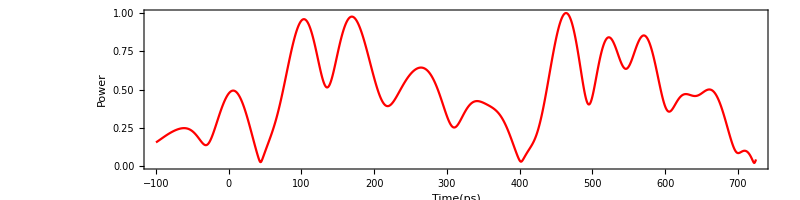

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

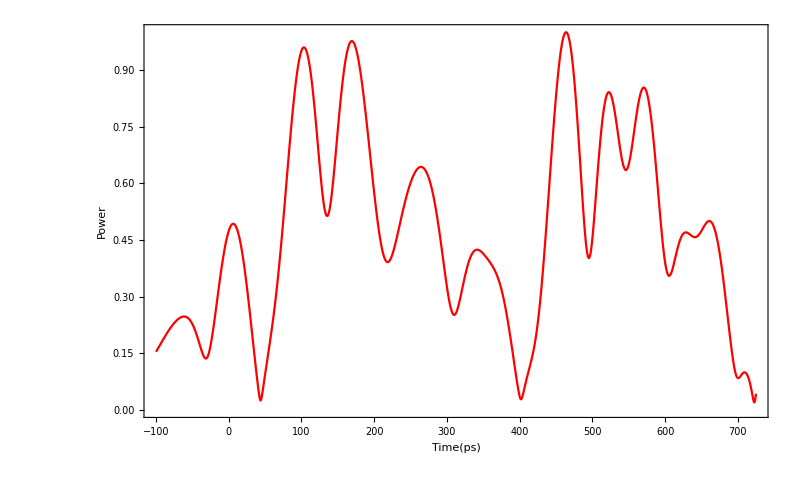

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

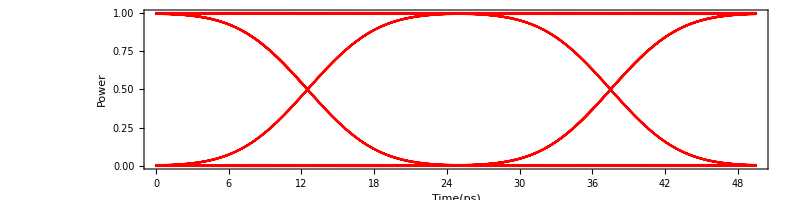

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

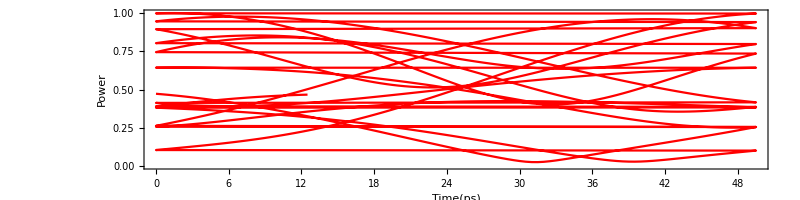

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 82 point

0 is 50 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.63755

Average of 0 is 0.320802

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.113133

A Standard Deviation of 0 is 0.157381

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

General::munfl: Exp[-1240.54]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

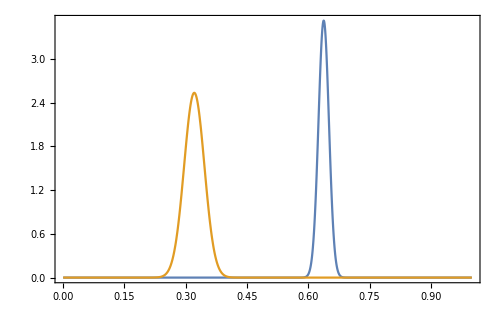

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 1.17091

Q-dB is 1.37048 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 0.120817

Eye Opening is 0.145964

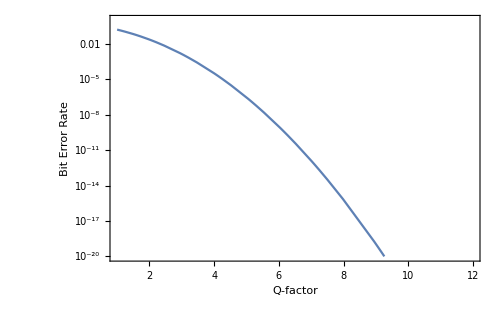

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```